# GetCircuitsFromChannel

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"] // Quiet;
CreateLocalQuESTEnv["../quest_link"];
```

## Doc

```mathematica
?GetCircuitsFromChannel
```

## Correctness

## Decomposition

### Unitary mixtures

```mathematica
GetCircuitsFromChannel @ Subscript[Deph, 0][x]
DrawCircuit @ %
```

{{Fac[√(1-x)]},{Fac[√x],Z_0}}

-Graphics-

{{Fac[√(1-x)]},{Fac[(√x)/(√3)],Z_0},{Fac[(√x)/(√3)],Z_1},{Fac[(√x)/(√3)],Z_0,Z_1}}

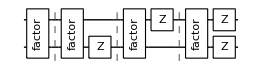

```mathematica
GetCircuitsFromChannel @ Subscript[Deph, 0,1][x]
DrawCircuit @ %
```

{{Fac[√(1-x)]},{Fac[(√x)/(√3)],X_0},{Fac[(√x)/(√3)],Y_0},{Fac[(√x)/(√3)],Z_0}}

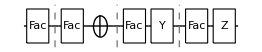

```mathematica
GetCircuitsFromChannel @ Subscript[Depol, 0][x]
DrawCircuit @ %
```

{{Fac[√(1-x)]},{Fac[(√x)/(√15)],X_1},{Fac[(√x)/(√15)],Y_1},{Fac[(√x)/(√15)],Z_1},{Fac[(√x)/(√15)],X_0},{Fac[(√x)/(√15)],X_0,X_1},{Fac[(√x)/(√15)],X_0,Y_1},{Fac[(√x)/(√15)],X_0,Z_1},{Fac[(√x)/(√15)],Y_0},{Fac[(√x)/(√15)],Y_0,X_1},{Fac[(√x)/(√15)],Y_0,Y_1},{Fac[(√x)/(√15)],Y_0,Z_1},{Fac[(√x)/(√15)],Z_0},{Fac[(√x)/(√15)],Z_0,X_1},{Fac[(√x)/(√15)],Z_0,Y_1},{Fac[(√x)/(√15)],Z_0,Z_1}}

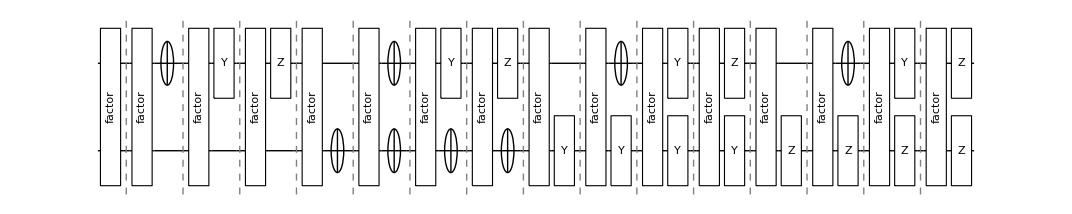

```mathematica
GetCircuitsFromChannel @ Subscript[Depol, 0,1][x]
DrawCircuit @ %
```

### Non-mixtures

```mathematica
GetCircuitsFromChannel @ Subscript[Damp, 0][x]
```

{{Matr_0[{{1,0},{0,√(1-x)}}]},{Matr_0[{{0,√x},{0,0}}]}}

```mathematica
GetCircuitsFromChannel @ Subscript[Kraus, 0] @ { ({{a, b}, {c, d}}), ({{e, f}, {g, h}})}
```

{{Matr_0[{{a,b},{c,d}}]},{Matr_0[{{e,f},{g,h}}]}}

### Circuits

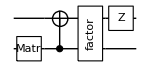
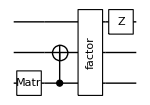
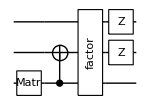
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawCircuit /@ GetCircuitsFromChannel @ Circuit[Subscript[Damp, 0][x] Subscript[C, 0][Subscript[X, 1]]Subscript[Deph, 1,2][y]]
```

### Unitaries

```mathematica
in = Circuit[G[x]Fac[.1] Subscript[H, 0] Subscript[Id, 1] Subscript[Ph, 0,1][x]R[.1,Subscript[X, 0] Subscript[Z, 1]]Subscript[C, 0,1][Subscript[Rx, 2][x]] Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2] Subscript[SWAP, 0,1] Subscript[T, 0] Subscript[S, 1]];
out = GetCircuitsFromChannel[in];
in === Flatten @ out
```

True

## Expectation values

```mathematica
test[channels_] := Module[
	{circs, n, h, ψi, ψ, ϕ, ρ, ω, e1, e2, err},
	
	(* use random Pauli observable *)
	n = 1 + Max @ GetCircuitQubits[channels];
	h = GetRandomPauliString[n];
	
	(* use random initial state *)
	ψi = CreateQureg[n];
	SetQuregMatrix[ψi, RandomComplex[{0,1+ⅈ}, 2^n]];
	
	(* use QuESTlink's numerical backend to... *)
	{ψ,ϕ} = CreateQuregs[n, 2];
	{ρ,ω} = CreateDensityQuregs[n, 2];
	
	(* compute expec value via channels upon density matrix ...*)
	InitPureState[ρ, ψi];
	ApplyCircuit[ρ, channels];
	e1 = CalcExpecPauliString[ρ, h, ω];
	
	(* and via decomposed circuits upon statevector... *)
	circs = GetCircuitsFromChannel[channels];
	e2 = Sum[
		InitPureState[ψ, ψi];
		ApplyCircuit[ψ, circ];
		CalcExpecPauliString[ψ, h, ϕ],
		{circ, circs}];
		
	(* clean up *)
	DestroyAllQuregs[];
		
	err = e1 - e2 // Abs // Chop;
	Echo[Length[circs], "Number of decomposed circuits:"];
	Echo[err, "error: "];
	If[err =!= 0, Style["ERRONEOUS DECOMPOSITION!", Red]]
]
```

### Unitary mixtures

```mathematica
test[Subscript[Deph, 0] @ RandomReal[{0,1/2}]]
```

Number of decomposed circuits:  2

error:   0

```mathematica
test[Subscript[Depol, 0] @ RandomReal[{0,3/4}]]
```

Number of decomposed circuits:  4

error:   0

```mathematica
test[Subscript[Deph, 0,1] @ RandomReal[{0,3/4}]]
```

Number of decomposed circuits:  4

error:   0

```mathematica
test[Subscript[Depol, 0,1] @ RandomReal[{0,15/16}]]
```

Number of decomposed circuits:  16

error:   0

### Non-mixtures

```mathematica
test[Subscript[Damp, 0] @ RandomReal[]]
```

Number of decomposed circuits:  2

error:   0

```mathematica
k = Table[RandomVariate @ CircularUnitaryMatrixDistribution[2], 3];
test[Subscript[KrausNonTP, 0][k]]
```

Number of decomposed circuits:  3

error:   0

```mathematica
k = Table[RandomVariate @ CircularUnitaryMatrixDistribution[4], 10];
test[Subscript[KrausNonTP, 0,1][k]]
```

Number of decomposed circuits:  10

error:   0

```mathematica
k = Table[RandomComplex[{-1-ⅈ,1+ⅈ}, {2^2,2^2}], 15];
test[Subscript[KrausNonTP, 0,1][k]]
```

Number of decomposed circuits:  15

error:   0

### Circuits

```mathematica
in = Circuit[Subscript[H, 0] Subscript[Damp, 0][.1]R[.1,Subscript[X, 0] Subscript[Z, 1]]Subscript[Deph, 0,1][.3]Subscript[C, 0,1][Subscript[Rx, 2][.9]]Subscript[Depol, 1][.3] Subscript[SWAP, 0,1] Subscript[T, 0] Subscript[Depol, 0,1][.3] Subscript[S, 1]];
test[in]
```

Number of decomposed circuits:  512

error:   0

## Errors

```mathematica
GetCircuitsFromChannel[a]
```

GetCircuitsFromChannel::error: Invalid arguments. See ?GetCircuitsFromChannel

$Failed

```mathematica
GetCircuitsFromChannel[Subscript[X, 0],b]
```

GetCircuitsFromChannel::error: Invalid arguments. See ?GetCircuitsFromChannel

$Failed